```mathematica
L=40;
tab=Table[{x,1/((L/π)Sin[x π/L])^(1/4)},{x,1,L/2}];
```

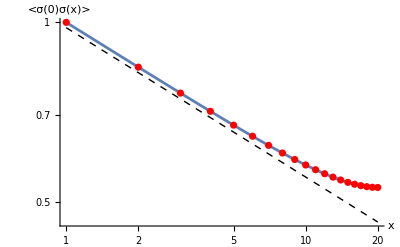

```mathematica
Show[LogLogPlot[0.98/(y)^(1/4),{y,1,20},PlotStyle->{Black,Dashed,Thin}],LogLogPlot[1/((L/π)Sin[x π/L])^(1/4),{x,1,20}],ListLogLogPlot[tab, PlotStyle->Red],AxesLabel->{"x","<σ(0)σ(x)>"}]
```

```mathematica
L=40;
tab=Table[{(L/π)Sin[x π/L],1/((L/π)Sin[x π/L])^(1/4)},{x,1,L/2}];
```

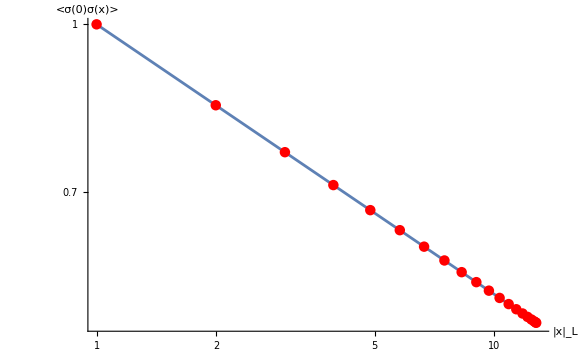

```mathematica
Show[LogLogPlot[1/y^(1/4),{y,1,13}],ListLogLogPlot[tab, PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"}]
```